# Polarization

Malcolm Levitt & Christian Bengs 01-July-2023
This documentation applies to SpinDynamica v3.10

more advanced topics use this colour

SpinDynamica contains some specialized routines for the handling and analysis of strongly polarized spin systems

## Setup

The code in this notebook requires the installation and initialization of SpinDynamica, as described in part 1 of the documentation

```mathematica
Needs["SpinDynamica`"];
SetSpinSystem[3];
```

SpinDynamica version SDv3.10.0 loaded by Mathematica 14.2 running on Mac OS X ARM (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Dot,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

SpinDynamica::badinfo: In some cases, requesting information by executing "?<symbol>") generates an infinite loop. I have not been able to identify why this happens. In these cases, readable information on a symbol may be generated by executing "<symbol>::usage". Apologies from MHL.

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

## Polarized density operators

The routines PolarizedDensityOperator and SingletPolarizedDensityOperator set up ensemble density operators with arbitrary polarization levels.

### PolarizedDensityOperator

PolarizedDensityOperator is used to set up a density operator with a specified degree of oriented spin angular momentum along an arbitrary axis. By default, the z-axis is chosen, and the default polarization level is 1.

In the 3-spin example below, PolarizedDensityOperator[ ] generates a density operator with maximum polarization along the z-axis:

```mathematica
PolarizedDensityOperator[]
```

1/8 (4 (I_(1z)•I_(2z))+4 (I_(1z)•I_(3z))+4 (I_(2z)•I_(3z))+8 (I_(1z)•I_(2z)•I_(3z))+2 I_(1z)+2 I_(2z)+2 I_(3z)+𝟙)

Note that the density operator does not consist purely of z-terms, but also double and triple products of z-operators. This is correct. The matrix representation of this operator shows that all spins are in the |ααα> state:

```mathematica
MatrixRepresentation[PolarizedDensityOperator[]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

A lower polarization level, or a symbolic polarization level, may be specified:

```mathematica
PolarizedDensityOperator[p]
```

1/8 (4 p^2 (I_(1z)•I_(2z))+4 p^2 (I_(1z)•I_(3z))+4 p^2 (I_(2z)•I_(3z))+8 p^3 (I_(1z)•I_(2z)•I_(3z))+2 p I_(1z)+2 p I_(2z)+2 p I_(3z)+𝟙)

```mathematica
PolarizedDensityOperator[0.01]
```

0.00005 (I_(1z)•I_(2z))+0.00005 (I_(1z)•I_(3z))+0.00005 (I_(2z)•I_(3z))+1.×10^-6 (I_(1z)•I_(2z)•I_(3z))+0.0025 I_(1z)+0.0025 I_(2z)+0.0025 I_(3z)+𝟙/8

Note that the quadratic and higher terms scale with powers of the polarization level.

It is possible to specify the polarization axis:

```mathematica
PolarizedDensityOperator["y"]
```

1/8 (4 (I_(1y)•I_(2y))+4 (I_(1y)•I_(3y))+4 (I_(2y)•I_(3y))+8 (I_(1y)•I_(2y)•I_(3y))+2 I_(1y)+2 I_(2y)+2 I_(3y)+𝟙)

```mathematica
PolarizedDensityOperator[{0.1,"y"}]
```

1/8 (4 (I_(1z)•I_(2z))+4 (I_(1z)•I_(3z))+4 (I_(2z)•I_(3z))+8 (I_(1z)•I_(2z)•I_(3z))+2 I_(1z)+2 I_(2z)+2 I_(3z)+𝟙)

It is possible to specify a subset of spins in the current spin system which are polarized:

```mathematica
PolarizedDensityOperator[{1,2}]
```

1/8 (4 (I_(1z)•I_(2z))+2 I_(1z)+2 I_(2z)+𝟙)

```mathematica
PolarizedDensityOperator[{1,2},{0.1,"y"}]
```

0.005 (I_(1y)•I_(2y))+0.025 I_(1y)+0.025 I_(2y)+𝟙/8

```mathematica
PolarizedDensityOperator[{1,2},"z"]
```

1/8 (4 (I_(1z)•I_(2z))+2 I_(1z)+2 I_(2z)+𝟙)

### SingletPolarizedDensityOperator

SingletPolarizedDensityOperator is used to set up a density operator with a specified degree of singlet polarization for a set of spin pairs, or several spin pairs.

In the 2-spin example below, SingletPolarizedDensityOperator[ ] generates a density operator with maximum singlet polarization:

```mathematica
SetSpinSystem[2];
SingletPolarizedDensityOperator[]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

1/4 (-4 ((I⃗)_1•(I⃗)_2)+𝟙)

The matrix representation of this in the SingletTripletBasis shows that only the singlet state is populated:

```mathematica
MatrixRepresentation[SingletPolarizedDensityOperator[],SingletTripletBasis[]]//MatrixForm
BasisKets[SingletTripletBasis[]]⟦1⟧
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(-|βα⟩+|αβ⟩)/(√2)

A lower polarization level, or a symbolic polarization level, may be specified:

```mathematica
SingletPolarizedDensityOperator[p]
```

1/4 (-4 p ((I⃗)_1•(I⃗)_2)+𝟙)

```mathematica
MatrixRepresentation[SingletPolarizedDensityOperator[p],SingletTripletBasis[]]//MatrixForm
```

(1/4 (1+3 p) | 0 | 0 | 0
0 | (1-p)/4 | 0 | 0
0 | 0 | (1-p)/4 | 0
0 | 0 | 0 | (1-p)/4)

The maximum singlet polarization is +1, and the minimum is -1/3:

```mathematica
SingletPolarizedDensityOperator[-1/2]
```

SingletPolarizedDensityOperator::toonegpol: The singlet polarization cannot be less than -1/3.

$Failed

The minimum value corresponds to complete singlet depletion at the expense of the triplet states:

```mathematica
SingletPolarizedDensityOperator[-1/3]
MatrixRepresentation[%,SingletTripletBasis[]]//MatrixForm
```

1/3 ((I⃗)_1•(I⃗)_2)+𝟙/4

(0 | 0 | 0 | 0
0 | 1/3 | 0 | 0
0 | 0 | 1/3 | 0
0 | 0 | 0 | 1/3)

In higher spin systems, the relevant spin pair must be specified:

```mathematica
SetSpinSystem[3]
SingletPolarizedDensityOperator[{1,2}]
SingletPolarizedDensityOperator[{{1,2},p}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

1/8 (-4 ((I⃗)_1•(I⃗)_2)+𝟙)

1/8 (-4 p ((I⃗)_1•(I⃗)_2)+𝟙)

If there are enough spins, one can specify different singlet polarizations for different spin pairs:

```mathematica
SetSpinSystem[4]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

```mathematica
SingletPolarizedDensityOperator[{{1,2},{3,4}}]
```

1/16 (16 (((I⃗)_1•(I⃗)_2)•((I⃗)_3•(I⃗)_4))-4 ((I⃗)_1•(I⃗)_2)-4 ((I⃗)_3•(I⃗)_4)+𝟙)

```mathematica
SingletPolarizedDensityOperator[{{{1,2},1},{{3,4},-1/3}}]
```

1/48 (-16 (((I⃗)_1•(I⃗)_2)•((I⃗)_3•(I⃗)_4))-12 ((I⃗)_1•(I⃗)_2)+4 ((I⃗)_3•(I⃗)_4)+3 𝟙)

## Polarization levels

The routines PolarizationLevelOperator and SingletPolarizationLevelOperator may be used to determine the level of polarization from a given density operator. They may also be used to simulate the polarization level under a sequence of events.

### determining the polarization levels of a density operator

A given density operator may be projected onto a PolarizationLevelOperator[..] to determine the corresponding degree of spin orientation along a certain axis.

For example, consider the following density operator, which corresponds to full polarization along the z-axis

```mathematica
SetSpinSystem[3];
ρ=PolarizedDensityOperator[]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

1/8 (4 (I_(1z)•I_(2z))+4 (I_(1z)•I_(3z))+4 (I_(2z)•I_(3z))+8 (I_(1z)•I_(2z)•I_(3z))+2 I_(1z)+2 I_(2z)+2 I_(3z)+𝟙)

The degree of polarization along the z-axis may be verified as follows:

```mathematica
OperatorAmplitude[ρ-> PolarizationLevelOperator[]]
```

1

There is no polarization along the x-axis:

```mathematica
OperatorAmplitude[ρ-> PolarizationLevelOperator["x"]]
```

0

The polarization level of individual sets of spins may also be determined:

```mathematica
OperatorAmplitude[ρ-> PolarizationLevelOperator[1]]
OperatorAmplitude[ρ-> PolarizationLevelOperator[2]]
```

1

1

The mean polarization level of set of spins may be determined:

```mathematica
OperatorAmplitude[ρ-> PolarizationLevelOperator[{1,2}]]
```

1

To determine the level of SingletPolarization a given density operator may be projected onto a SingletPolarizationLevelOperator[..].

```mathematica
OperatorAmplitude[ρ-> SingletPolarizationLevelOperator[{1,2}]]
```

-1/3

The result is -1/3 since the singlet state is completely depleted if the spin system is completely polarized.

PolarizationLevelOperators may also be used for determining the thermal equilibrium polarization level. The example below is for protons in a field of 11.4 T at 300 K.

```mathematica
SetSpinSystem[1];
ρeq=ThermalEquilibriumDensityOperator[LarmorFrequency[1,11.4] opI["z"],300]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Operator[<<..>>, OperatorType→Hermitian ]

```mathematica
OperatorAmplitude[ρeq-> PolarizationLevelOperator[]]
%//EngineeringForm
```

0.0000388245

38.8245×10^-6

This shows that the thermal polarization level of nuclear spins is very small.

### simulating polarization levels

The symbols PolarizationLevelOperator and SingletPolarizationLevelOperator may also be used in the simulation routines Trajectory, TransformationAmplitude, TransformationAmplitudeTable, and Signal1D.

In the example below, the system is prepared in a completely polarized state, and an rf field is applied to rotate the polarization. The evolution of the polarization level is followed using Trajectory.

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

TrajectoryFunction[{{0,1.}}, <>]

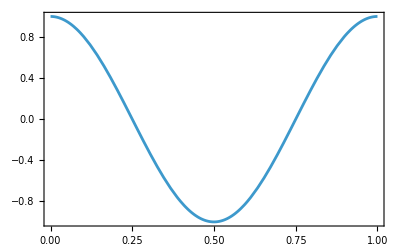

```mathematica
SetSpinSystem[1];
Trajectory[
PolarizedDensityOperator[]->PolarizationLevelOperator[],
{2π opI["x"],1}
]
Plot[%[t],{t,0,1}]
```

In the example below, a 2-spin-1/2 system is prepared in a fully polarized state, and a rf field is applied to just one of the spins. The simulation shows how the polarization level and singlet polarization level evolve:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

{TrajectoryFunction[{{0,1.}}, <>],TrajectoryFunction[{{0,1.}}, <>]}

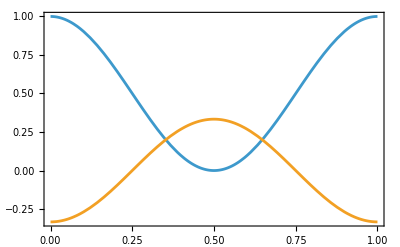

```mathematica
SetSpinSystem[2];
{ztraj,straj}=Trajectory[
PolarizedDensityOperator[]->{PolarizationLevelOperator[],SingletPolarizationLevelOperator[]},
{2π opI[1,"x"],1}
]
Plot[{ztraj[t],straj[t]},{t,0,1}]
```

The singlet polarization level is modulated since the selective rf field on just one of the coupled spins converts singlet population into triplet population, and back again.